1 - 8 Scalar fields in the plane
Let the temperature T in a body be independent of z so that it is given by a scalar function T = T(x, t). Identify the isotherms T(x, y) = const. Sketch some of them.

1.  T=x^2-y^2

```mathematica
Clear["Global`*"]
```

Below: Some of the isotherms are shown, (8). The idea behind the controllable plane is that changing the altitude of the grid strengthens awareness about the behavior of the function in its volume.

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{x^2-y^2},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,-4.00},-4,4,Appearance->"Labeled"}]
```

2. T=xy.

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{x y},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,0.00},-4,4,Appearance->"Labeled"}]
```

3.  T = 3 x - 4 y

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{3x-4 y},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,-10.00},-12,12,Appearance->"Labeled"}]
```

5.  T=y/(x^2+y^2)

```mathematica
Clear["Global`*"]
```

Below: this one goes into a strange shape-shifting mode while the slider is being manipulated.

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{y/(y^2+x^2)},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,-1.99},-1.9,2.1,Appearance->"Labeled"}]
```

6.  T=x/(x^2+y^2)

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{x/(y^2+x^2)},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,-2.00},-2.1,2,Appearance->"Labeled"}]
```

7.  T=9 x^2+4 y^2

```mathematica
Clear["Global`*"]
```

```mathematica
Manipulate[v1={1,0,0};
v2={0,1,0};
p0={0,0,c};
plane1=p0+s*v1+t*v2;
Show[Plot3D[{9 x^2+4 y^2},{x,-2,2},{y,-2,2},Mesh->8,MeshFunctions->{#3&},FaceGrids->{{0,-1,0}},ColorFunction->Function[{x,y,z},Hue[z]],ColorFunctionScaling->True,MeshShading->{Red,Green,Blue,Yellow,Pink,Brown,Orange,Purple}],
Plot3D[{plane1},{x,-2,2},{y,-2,2},PlotStyle->Directive[RGBColor[1,0.5,0.35,1],Opacity[0.3]],MeshStyle->Black,Mesh->20]],
{{c,-1.},-1,50,Appearance->"Labeled"}]
```

8.  CAS project. Scalar fields in the plane. Sketch or graph isotherms of the following fields and describe what they look like.

(a) x^2-4x-y^2

```mathematica
Clear["Global`*"]
```

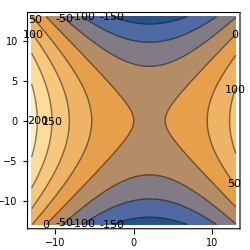

```mathematica
ContourPlot[x^2-4 x-y^2,{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

(b) x^2 y-y^3/3

```mathematica
Clear["Global`*"]
```

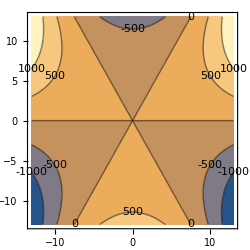

```mathematica
ContourPlot[x^2 y-y^3/3,{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[x^2 y-y^3/3,{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

(c) Cos[x] Sinh[y]

```mathematica
Clear["Global`*"]
```

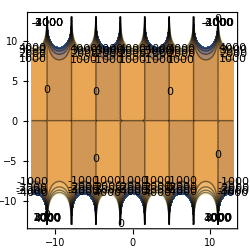

```mathematica
ContourPlot[Cos[x] Sinh[y],{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[Cos[x] Sinh[y],{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

(d) Sin[x] Sinh[y]

```mathematica
Clear["Global`*"]
```

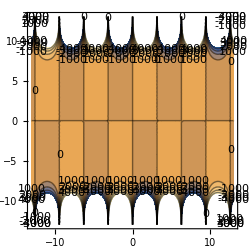

```mathematica
ContourPlot[Sin[x] Sinh[y],{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[Sin[x] Sinh[y],{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

(e) ⅇ^x Sin[y]

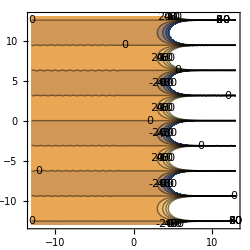

```mathematica
ContourPlot[Exp[x] Sin[y],{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[Exp[x] Sin[y],{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

```mathematica
Clear["Global`*"]
```

(f) ⅇ^(2x)Cos[2y]

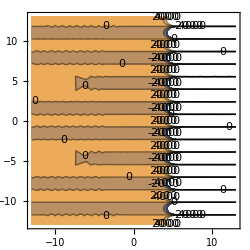

```mathematica
ContourPlot[Exp[2 x] Cos[2 y],{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[Exp[2 x] Cos[2 y],{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics3D-

(g) x^4-6 x^2 y^2+y^4

```mathematica
Clear["Global`*"]
```

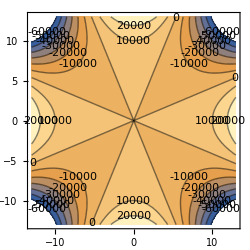

```mathematica
ContourPlot[x^4-6 x^2 y^2+y^4,{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[x^4-6 x^2 y^2+y^4,{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->300]
```

-Graphics3D-

(h) x^2-2x-y^2

```mathematica
Clear["Global`*"]
```

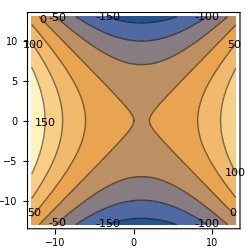

```mathematica
ContourPlot[x^2-2 x-y^2,{x,-13,13},{y,-13,13},ContourLabels->True,ImageSize->250]
```

```mathematica
Plot3D[x^2-2 x-y^2,{x,-13,13},{y,-13,13},ColorFunction->"Rainbow",PlotLegends->Automatic,ImageSize->250]
```

-Graphics3D-

9 - 14 Scalar fields in space
What kind of surfaces are the level surfaces f(x, y, z) = const?

9.  f = 4 x - 3 y + 2 z

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[4 x-3 y+2 z,{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

10.  f=9(x^2+y^2)+z^2

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[9 (x^2+y^2)+z^2,{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

11. f=5 x^2+2 y^2

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[5 x^2+2 y^2,{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

12.  f=z-√(x^2+y^2)

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[z-√(x^2+y^2),{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

13.  f=z-(x^2+y^2)

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[z-(x^2+y^2),{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

14.  f=x-y^2

```mathematica
Clear["Global`*"]
```

```mathematica
ContourPlot3D[x^2-y^2,{x,-13,13},{y,-13,13},{z,-13,13},ImageSize->250]
```

-Graphics3D-

15 - 20 Vector fields
Sketch figures similar to figure 198, p. 378. Try to interpret the field of v as a velocity field.

15.  v = i + j

```mathematica
Clear["Global`*"]
```

Let me see if I can use the verbiage in problem 19 (which was worked first) to find the right expression for this function. 
	v=i+j=1[1,0,0]+1[0,1,0]+0[0,0,1]=[1,1,0]
Then to apply the recipe to an input vector. Here z and k are ignored, because according to the problem expression, these contribute nothing to the final output. Also, no x or y factors are visible in the problem expression. So again I am operating on an input vector of the form [x,y,0]. What comes out of the function machine is [x+1,y+1,0]

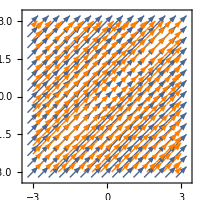

```mathematica
StreamPlot[{1,1},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

17.  v = xj

```mathematica
Clear["Global`*"]
```

Let me see if I can again use the verbiage in problem 19 to find the right expression for this function. 
	v=xj=0[1,0,0]+x[0,1,0]+0[0,0,1]=[0,x,0]
Then to apply the recipe to an input vector. Here z and k are ignored, because according to the problem expression, these contribute nothing to the final output. However, x is visible in the expression and must be used, I believe. So again I am operating on an input vector of the form [x,y,0]. What comes out of the function machine is [x,x+y,0]

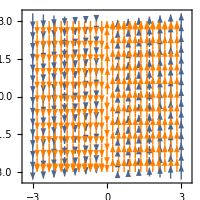

```mathematica
StreamPlot[{0,x},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

19.  v = xi - yj

```mathematica
Clear["Global`*"]
```

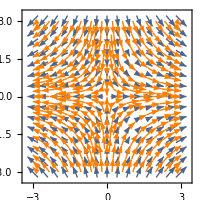

```mathematica
StreamPlot[{x,- y},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

This one is in the s.m.. Maybe I can summarize. First is written the function definition in terms of i, j, k. Thus, v=v(x,y,z)=xi-yj+0k. This makes sense, with regard to the third coordinate. There is no mention of k, so it must be treated as zero. Then the function is expanded,
	v=xi-yj=x[1,0,0]-y[0,1,0]=[x,0,0]-[0,y,0]=[x,-y,0],
ending up with a recipe for the function’s operation on an operand vector. The s.m. describes what it means for a vector function to operate. A starting vector is transformed into the output vector by the function recipe. In this case, if I take a sample vector [x,y,0] and feed it to the function, it adds to it. In effect, I get [x,y,0]+[x,-y,0]=[2x,0,0].

The thing that comes out is not how the function is shown in printed form, however.  It is not what the plot command sees. What the plot command sees is the expression at the end of the sequence of equalities above.

21. CAS project. Vector fields. Plot by arrows:

(a) v={x, x^2} | (b)v={1/y, 1/x}
(c)v={Cos[x],Sin[x]} | (d)v=ⅇ^(-(x^2+y^2)){x,-y}

```mathematica
Clear["Global`*"]
```

For (a):

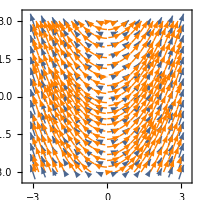

```mathematica
StreamPlot[{x,x^2},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

For (b):

```mathematica
Clear["Global`*"]
```

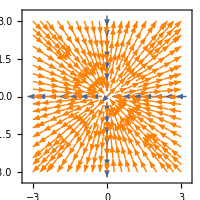

```mathematica
StreamPlot[{1/y,1/x},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

For (c):

```mathematica
Clear["Global`*"]
```

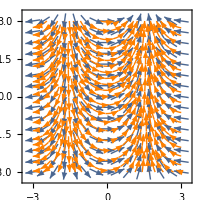

```mathematica
StreamPlot[{Cos[x],Sin[x]},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```

For (d):

```mathematica
Clear["Global`*"]
```

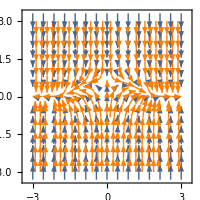

```mathematica
StreamPlot[{Exp[-(x^2+y^2)] x,Exp[-(x^2+y^2)] -y},{x,-3,3},{y,-3,3},VectorPoints->Automatic,StreamStyle->Orange,ImageSize->200]
```